```mathematica
fitO := o + (1/2)*y + 2*B;
fitY := a*o + y + b*B;
fitB := o*(1/2) + 2*y + B;

fitmedio := fitO * o + fitY * y + fitB * B;

dodt := o * (fitO - fitmedio);
dydt := y * (fitY - fitmedio);
dbdt := B * (fitB - fitmedio);

equilibrio = Solve[{dodt == 0, dydt == 0, dbdt == 0, o + y + B ==1}, {o, y, B}]
```

{{o→1,y→0,B→0},{o→0,y→0,B→1},{o→2,y→0,B→-1},{o→0,y→1,B→0},{o→1/(3-2 a),y→(2 (-1+a))/(-3+2 a),B→0},{o→-(2 (-5+3 b))/(5+10 a-8 b),y→(2 (2 a-b))/(5+10 a-8 b),B→(-5+6 a)/(5+10 a-8 b)},{o→0,y→(-1+b)/b,B→1/b}}

```mathematica
jacobiana=FullSimplify[D[{dodt,dydt,dbdt},{{o,y,B}}]];
MatrixForm[jacobiana]
```

(1/2 (4 o+y-2 (B^2+3 o^2+y^2+o (y+2 a y)+B (-2+5 o+(2+b) y))) | -1/2 o (-1+2 (2+b) B+o+2 a o+4 y) | -1/2 o (-4+4 B+5 o+2 (2+b) y)
-1/2 y (5 B+4 o+2 a (-1+y)+y) | b B-B^2+a o-(5 B o)/2-o^2-(-2+2 (2+b) B+o+2 a o) y-3 y^2 | y (b-2 B-(5 o)/2-2 y-b y)
-1/2 B (-1+5 B+4 o+y+2 a y) | -1/2 B (-4+2 (2+b) B+o+2 a o+4 y) | -3 B^2-o^2-(-2+y) y-1/2 o (-1+y+2 a y)-B (-2+5 o+2 (2+b) y))

```mathematica
mat1=jacobiana/. {o->1/(3-2 a),y->(2 (-1+a))/(-3+2 a),B->0};
autovalores1=Eigenvalues[mat1]
Resolve[Exists[{a,b},a>=1&&b>=0 && b <=1&& a-b>=0 && Max[Re[autovalores1]]<0]]
Reduce[a>=1&&b>=0 && b <=1&& a-b>=0 && Max[Re[autovalores1]]<0,{a,b},Reals]
```

{(-5+6 a)/(2 (-3+2 a)),-(6-7 a+2 a^2)/(-3+2 a)^2,(3-5 a+2 a^2)/(-3+2 a)^2}

True

1<a<3/2&&0≤b≤1

```mathematica
mat2=jacobiana/. {o->0,y->(-1+b)/b,B->1/b};
autovalores2=Eigenvalues[mat2]
Resolve[Exists[{a,b},a>=1&&b>=0 && b<= 1 && a-b>=0 && Max[Re[autovalores2]]<0]]
Reduce[a>=1&&b>=0 && b <=1&& a-b>=0 && Max[Re[autovalores2]]<0,{a,b},Reals]
```

{-(-5+3 b)/(2 b),-(-b^5+b^6)/b^6,-(-b^5+2 b^6)/b^6}

False

False

```mathematica
mat3=jacobiana/. {o->-(2 (-5+3 b))/(5+10 a-8 b),y->(2 (2 a-b))/(5+10 a-8 b),B->(-5+6 a)/(5+10 a-8 b)};
autovalores3=Eigenvalues[mat3]
Resolve[Exists[{a,b},a>=1&&b>=0 && b <=1&& a-b>=0 && Max[Re[autovalores3]]<0], Reals]
Reduce[a>=1&&b>=0 && b <=1&& a-b>=0 && Max[Re[autovalores3]]<0,{a,b},Reals]
```

{-(7 (10 a+20 a^2-5 b-26 a b+8 b^2))/(5+10 a-8 b)^2,(25+30 a-40 a^2-45 b+22 a b+8 b^2-(5+10 a-8 b) √(25+160 a-224 a^2-110 b+8 a b+144 a^2 b+61 b^2-72 a b^2))/(2 (5+10 a-8 b)^2),(25+30 a-40 a^2-45 b+22 a b+8 b^2+(5+10 a-8 b) √(25+160 a-224 a^2-110 b+8 a b+144 a^2 b+61 b^2-72 a b^2))/(2 (5+10 a-8 b)^2)}

False

False

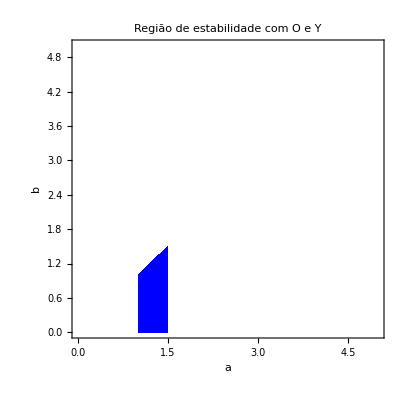

```mathematica
region1 = Reduce[a>=1&&b>=0 && a-b>=0 && Max[Re[autovalores1]]<0,{a,b},Reals];
RegionPlot[region1&&Max[Re[autovalores1]]<0,
{a,0,5},{b,0,5},
PlotStyle->{Blue,Opacity[1]},
BoundaryStyle->None,
PlotLegends->"Expressions",
FrameLabel->{"a","b"},
PlotLabel->"Região de estabilidade com O e Y"]
```

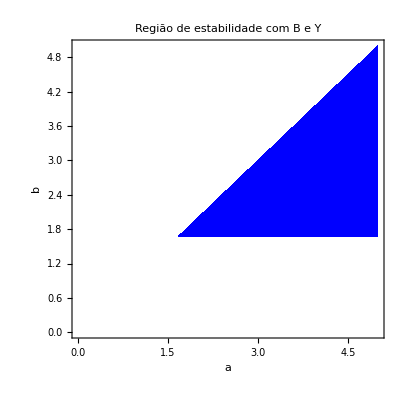

```mathematica
region2 = Reduce[a>=1&&b>=0 && a-b>=0 && Max[Re[autovalores2]]<0,{a,b},Reals];
RegionPlot[region2&&Max[Re[autovalores2]]<0,
{a,0,5},{b,0,5},
PlotStyle->{Blue,Opacity[1]},
BoundaryStyle->None,
PlotLegends->"Expressions",
FrameLabel->{"a","b"},
PlotLabel->"Região de estabilidade com B e Y"]
```

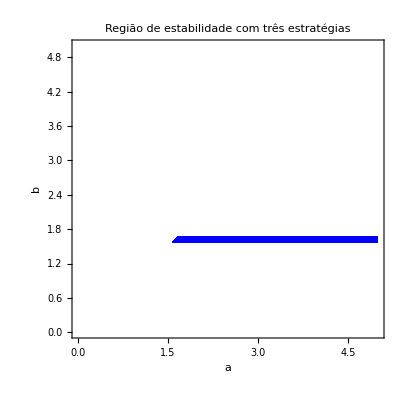

```mathematica
region3 = Reduce[a>=1&&b>=0 && a-b>=0 && Max[Re[autovalores3]]<0,{a,b},Reals];
RegionPlot[region3&&Max[Re[autovalores3]]<0,
{a,0,5},{b,0,5},
PlotStyle->{Blue,Opacity[1]},
BoundaryStyle->None,
PlotLegends->"Expressions",
FrameLabel->{"a","b"},
PlotLabel->"Região de estabilidade com três estratégias"]
```

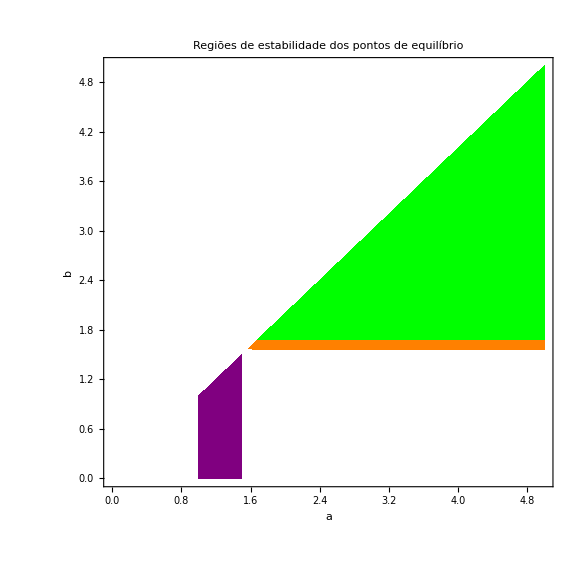

```mathematica
(*Ponto O e Y*)
plotOY=RegionPlot[region1&&Max[Re[autovalores1]]<0,
{a,0,5},{b,0,5},
PlotStyle->{Purple,Opacity[1]},
BoundaryStyle->None,
PlotLabel->Placed[{"Região de estabilidade com O e Y"}, Bellow]];

(*Ponto com B e Y*)
plotBY=RegionPlot[region2&&Max[Re[autovalores2]]<0,
{a,0,5},{b,0,5},
PlotStyle->{Green,Opacity[1]},
BoundaryStyle->None,
PlotLabel->Placed[{"Região de estabilidade com B e Y"}, Bellow]];

plotcoexistence=RegionPlot[region3&&Max[Re[autovalores3]]<0,
{a,0,5},{b,0,5},
PlotStyle->{Orange,Opacity[1]},
BoundaryStyle->None,
PlotLabel->Placed[{"Região de estabilidade com três estratégias"}, Bellow]];

(*sobrepondo todos*)
Show[plotOY,plotBY,plotcoexistence, FrameLabel->{"a","b"},PlotLabel->"Regiões de estabilidade dos pontos de equilíbrio",ImageSize->Large]
```